# Solucion de las ec de MOG: a orden 1

condiciones inciales. unidades: metro, kg, año

```mathematica
t0=13.7*10^9;(*años*)
G0=6*Gn;
H0=73.5*3.154*10^7/(3.086*10^19);(*en 1/año*)
Vg=(0.07659537+0.0*0.07659537/100)*G0^2/(t0^2);
G00=0;
Gn=6.7*10^-11*(3.154*10^7)^2;(*en m3/(kg*año3)*)
a0=c*t0;
a00=H0*a0;
c=3*10^8*3.154*10^7;(*m/año*)
mu0=a0^-1;
mu00=0;
w0=1./Sqrt[12];
w00=0;
```

```mathematica
0.1/H0
```

1.45234×10^9

```mathematica
0.07659537+25*0.07659537/100
```

0.0957442

```mathematica
{Hsol,Gsol,rhosol,musol,wsol,bsol,dsol,fsol}=NDSolveValue[{(H[t])^2==8.*Pi*G[t]*rho[t]/3.-4.*Pi*(1+t)^2*(H[t])^2*((b[t]/G[t])^2+(d[t]/mu[t])^2-(f[t])^2)/3.+8.*Pi*Vg/(3.*(G[t])^2)-(1+t)(H[t])^2*b[t]/G[t],H[t]*(H[t]-(1+t)*H'[t])==-4.*Pi*G[t]*rho[t]/3.+8.*Pi*(1+t)^2*(H[t])^2*((b[t]/G[t])^2+(d[t]/mu[t])^2-(f[t])^2)/3.+8.*Pi*Vg/(3.*(G[t])^2)-(1+t)(H[t])^2b[t]/(2.*G[t])+(1+t)*H[t]*(b'[t]*H[t]*(1+t)+b[t]*H'[t]*(1+t)+b[t]*H[t])/(2.*G[t])-(-(1+t)*b[t]*H[t])^2/(G[t])^2,(1+t)*H[t]*(b'[t]*H[t]*(1+t)+b[t]*H'[t]*(1+t)+b[t]*H[t])-(1+t)*3.*(H[t])^2b[t]-3.*(-(1+t)H[t]*b[t])^2/(2.*G[t])+G[t]*(1+t)^2*(H[t])^2*((d[t]/mu[t])^2-(f[t])^2)+3.Vg/G[t]-3.G[t](H[t]*(2*H[t]-(1+t)H'[t]))/(8.*Pi)==0,(1+t)*H[t]*(H[t]*d'[t]*(1+t)+d[t]*H[t]+H'[t]*d[t]*(1+t))-3.*(H[t])^2*(1+t)*d[t]-((1+t)*H[t]*d[t])^2/mu[t]-(1+t)^2*(H[t])^2*b[t]*d[t]/G[t]==0,(1+t)*H[t]*(H[t]*f'[t]*(1+t)+f[t]*H[t]+H'[t]*f[t]*(1+t))-3.*(H[t])^2*(1+t)*f[t]-(1+t)^2*(H[t])^2*b[t]*f[t]/G[t]==0,G'[t]==b[t],mu'[t]==d[t],w'[t]==f[t],H[0]==H0,G[0]==G0,b[0]==0,w[0]==w0,f[0]==0,mu[0]==mu0,d[0]==0},{H,G,rho,mu,w,b,d,f},{t,0.000000000000000000000000000001,3}]
```

{                             -30
InterpolatingFunction[{{1. 10   , 3.}}, <>],                             -30
InterpolatingFunction[{{1. 10   , 3.}}, <>],                             -30
InterpolatingFunction[{{1. 10   , 3.}}, <>],                             -30
InterpolatingFunction[{{1. 10   , 3.}}, <>],                             -30
InterpolatingFunction[{{1. 10   , 3.}}, <>],                             -30
InterpolatingFunction[{{1. 10   , 3.}}, <>],                             -30
InterpolatingFunction[{{1. 10   , 3.}}, <>],                             -30
InterpolatingFunction[{{1. 10   , 3.}}, <>]}

```mathematica
Plot[musol[t]/mu0,{t,0,3}]
```

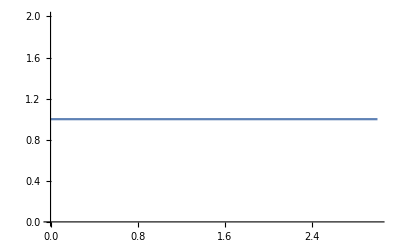

```mathematica
Plot[wsol[t]/w0,{t,0,3}]
```

-Graphics-

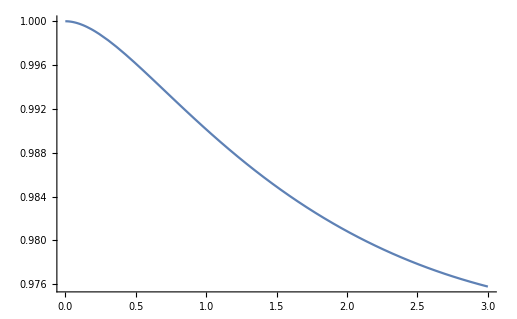

```mathematica
Plot[Gsol[t]/G0,{t,0,3}]
```

```mathematica
Export["Gsol735.dat",Table[{t,Gsol[t]/G0},{t,0,2.5,0.001}]]
```

Gsol735.dat

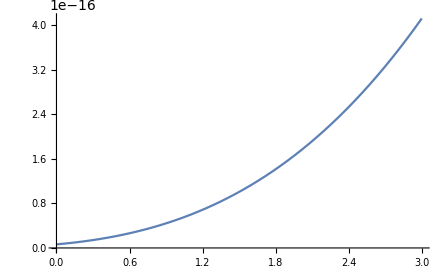

```mathematica
Plot[rhosol[t]/H0,{t,0,3}]
```

```mathematica
rhosol[0]
```

3.94633×10^-28

```mathematica
3.946333134197467*^-28*10^-3
```

3.94633×10^-31

```mathematica
0.303*1.06*10^-29
```

3.2118×10^-30

```mathematica
Hsol[0.4293] (*en 1/año*)
```

9.70289×10^-11

```mathematica
9.702886190744886*^-11*3.086*10^19/(3.154*10^7)
```

94.9369

# Integracion de H

```mathematica
NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->30,Method->"GlobalAdaptive",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->30,Method->"DoubleExponential",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->800,Method->"MonteCarlo",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->800,Method->"AdaptiveMonteCarlo",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->200,Method->"AdaptiveQuasiMonteCarlo",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->200,Method->"QuasiMonteCarlo",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->200,Method->"ClenshawCurtisRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->500,Method->"GaussKronrodRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->500,Method->"LobattoKronrodRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->500,Method->"LevinRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->500,Method->"MultipanelRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->500,Method->"NewtonCotesRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->200,Method->"RiemannRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,2.5},MaxRecursion->500,Method->"TrapezoidalRule",WorkingPrecision->15]
```

1.2732616451536

1.27326164515363

1.28585702848755

1.2780433781445

1.27326017821262

1.27278826329928

1.2732616451536

1.2732616451536

1.2732616451536

NIntegrate::nonlev: Integrand 7.358651976668826e-11 is not a Levin function.

NIntegrate::mtdfb: Numerical integration with "LevinRule" failed. The integration continues with Method -> "GaussKronrodRule".

1.2732616451536

1.2732616451536

1.2732616451536

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.27326455518027

1.27326164515299

```mathematica
NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->30,Method->"GlobalAdaptive",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->30,Method->"DoubleExponential",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->800,Method->"MonteCarlo",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->800,Method->"AdaptiveMonteCarlo",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->200,Method->"AdaptiveQuasiMonteCarlo",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->200,Method->"QuasiMonteCarlo",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->200,Method->"ClenshawCurtisRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->500,Method->"GaussKronrodRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->500,Method->"LobattoKronrodRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->500,Method->"LevinRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->500,Method->"MultipanelRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->500,Method->"NewtonCotesRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->200,Method->"RiemannRule",WorkingPrecision->15]

NIntegrate[1./(Hsol[t]/H0),{t,0,0.001},MaxRecursion->500,Method->"TrapezoidalRule",WorkingPrecision->15]
```

0.000999709315837529

0.000999709315837549

0.00099973584006773

0.00099972607051264

0.000999709315838116

0.000999708589110373

0.000999709315837529

0.000999709315837529

0.000999709315837528

NIntegrate::nonlev: Integrand 7.358651976668826e-11 is not a Levin function.

NIntegrate::mtdfb: Numerical integration with "LevinRule" failed. The integration continues with Method -> "GaussKronrodRule".

0.000999709315837529

0.000999709315837529

0.000999709315837529

0.000999711160183462

0.000999709315837529

# modulo de distancia

```mathematica
Export["H6737+25.dat",Table[{t,1./(Hsol[t]/H0)},{t,0,2.5,0.00001}]]
```

H6737+25.dat

```mathematica
Export["Hsol68745.dat",Table[{t,Hsol[t]},{t,0,2.5,0.01}]]
```

Hsol68745.dat

tengo chequeado que la tabla me la escribe bien. la informacion de z que tengo viene con hasta 6 decimales.

Prueba de la integral. Lo de adentro del log tiene que estar en Mpc:

```mathematica
mu[tcmb_]:=25+5*Log10[((1+tcmb)*(c/H0)*NIntegrate[1./(Hsol[t]/H0),{t,0,tcmb},MaxRecursion->30,Method->"GlobalAdaptive",WorkingPrecision->15])/(1000000*3.0857*10^16)]
```

```mathematica
NIntegrate[1./(Hsol[t]/H0),{t,0,3.0},MaxRecursion->30,Method->"GlobalAdaptive",WorkingPrecision->15]
```

1.38504188746619

```mathematica
NIntegrate[1./(Hsol[t]/H0),{t,0,2.98197},MaxRecursion->30,Method->"GlobalAdaptive",WorkingPrecision->15]
```

1.38136505140174

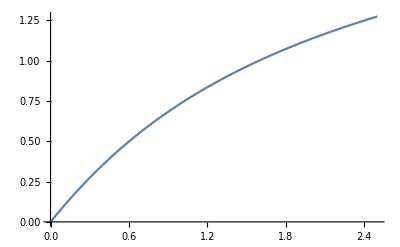

```mathematica
Plot[NIntegrate[1./(Hsol[t]/H0),{t,0,z},MaxRecursion->30,Method->"GlobalAdaptive",WorkingPrecision->15],{z,0,2.5}]
```

```mathematica
muuu=Table[mu[z],{z,0,2.5,0.05}];
```

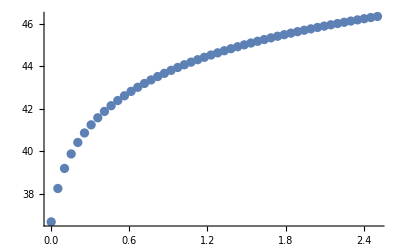

```mathematica
ListPlot[muuu,DataRange->{0.005,2.5}]
```

```mathematica
mu[0.01]
```

33.1144

Esta graficandolo medio raro. pero chequeando algunos puntos y la forma general pareceria ser coherente con la fig 11 del paper de Pantheon. Por lo cual podemos asumir que el calculo viene en la direccion correcta.